## Initialization

Load packages

```mathematica
$HistoryLength=1;
(*If package is installed to a non standard dir add it to path just in case*)
With[{pfn=ExpandFileName@FileNameJoin[{NotebookDirectory[],"..",".."}]},
If[!MemberQ[$Path,pfn], PrependTo[$Path,pfn]];
];
Needs["Developer`"]
Needs["DiffusiveDynamics`"]
(*Load the data on paralle Kernels*)
With[{path=$Path},
ParallelEvaluate[
$Path=path;(*add to the path of parallel Kernels*)
$HistoryLength=1;
Needs["Developer`"];
Needs["DiffusiveDynamics`"];
]];
$VerbosePrint=True;

R[α_]:={{Cos[α ],-Sin[α ]},{Sin[α ],Cos[α ]}};
DDD[Dx_,Dy_]:={{1/Dx^2,0},{0,1/Dy^2}};
D2DMat[Dx_,Dy_,α_]:=N[R[α °].DDD[Dx,Dy].Transpose[R[α °]]];

RotationMatrix
```

Define diffusion parameters

```mathematica
STEPS=2000000;
STEP=1;
CELLRANGE={1000.,500.};
ModI[x_,halfwidth_]:=Mod[x+halfwidth,2*halfwidth]-halfwidth;
ClearAll[DIFFX,DIFFY,DIFFA];
DIFFX=Compile[{x,y},
5Sin[x/ CELLRANGE[[1]] π] +10];
DIFFY=Compile[{x,y},
5Sin[y/ CELLRANGE[[2]] π] +10];
DIFFA=Compile[{x,y},
(((ModI[x,CELLRANGE[[1]]]/2)/CELLRANGE[[1]])^2+((ModI[y,CELLRANGE[[2]]]/2)/ CELLRANGE[[2]])^2)*180];

ClearAll[DIFFX,DIFFY,DIFFA];


DIFFX=Compile[{x,y},
1];
DIFFY=Compile[{x,y},
10];

DIFFA=Compile[{x,y},
45];
TENSOR[x_,y_]:=D2DMat[DIFFX[x,y],DIFFY[x,y],DIFFA[x,y]];
ClearAll[ENERGY]; (*energija v enotah kT*)
ENERGY=Compile[{x,y},1];
KT=1.;
CELL$plots=DiffusionParameters2DPlots[DIFFX,DIFFY,DIFFA,ENERGY,CELLRANGE]
StringForm["STEPS `1`; STEP `2`; KT `3`",STEPS,STEP,KT];
```

```mathematica
Plot3D[DIFFA[x,y],{x,-1*First@CELLRANGE,1*First@CELLRANGE},{y,-1*Last@CELLRANGE,1*Last@CELLRANGE},PlotPoints->100,MaxRecursion->5]
```

Generate Data

HERER!MultinormalDistribution

***GenerateDiffusionTrajectory2D***

***GenerateDiffusionTrajectory2D*** Options: 
   InitialPosition -> {0, 0}
   Verbose -> True
   VerboseLevel -> 5

DD:
CompiledFunction[{DiffusiveDynamics`Generate2D`Private`x$,DiffusiveDynamics`Generate2D`Private`y$},{{1,0},{0,10}},-CompiledCode-]

Nonrotated difusion tensor at {0,0}: {{1,0},{0,10}}

RotatedDD:
CompiledFunction[{DiffusiveDynamics`Generate2D`Private`x$,DiffusiveDynamics`Generate2D`Private`y$},{{5.5,-4.5},{-4.5,5.5}},-CompiledCode-]

Difusion tensor at {0,0}: {{5.5,-4.5},{-4.5,5.5}}

gradD:
CompiledFunction[{DiffusiveDynamics`Generate2D`Private`x$,DiffusiveDynamics`Generate2D`Private`y$},{0,0},-CompiledCode-]

gradient of D tensor at {0,0}: {0,0}

gradF:
CompiledFunction[{DiffusiveDynamics`Generate2D`Private`x$,DiffusiveDynamics`Generate2D`Private`y$},{0,0},-CompiledCode-]

gradient of free energy at {0,0}: {0,0}

stepfunction:
CompiledFunction[{DiffusiveDynamics`Generate2D`Private`xv,DiffusiveDynamics`Generate2D`Private`rv},Block[{DiffusiveDynamics`Generate2D`Private`x$7300=DiffusiveDynamics`Generate2D`Private`xv⟦1⟧,DiffusiveDynamics`Generate2D`Private`y$7300=DiffusiveDynamics`Generate2D`Private`xv⟦2⟧,DiffusiveDynamics`Generate2D`Private`g1$7300=DiffusiveDynamics`Generate2D`Private`rv⟦1⟧,DiffusiveDynamics`Generate2D`Private`g2$7300=DiffusiveDynamics`Generate2D`Private`rv⟦2⟧},{-1000.+Mod[1000.+2.94317 DiffusiveDynamics`Generate2D`Private`g1$7300-1.52896 DiffusiveDynamics`Generate2D`Private`g2$7300+DiffusiveDynamics`Generate2D`Private`x$7300,2000.],-500.+Mod[500.-1.52896 DiffusiveDynamics`Generate2D`Private`g1$7300+2.94317 DiffusiveDynamics`Generate2D`Private`g2$7300+DiffusiveDynamics`Generate2D`Private`y$7300,1000.]}],-CompiledCode-]

stepfunction at {0,0} and g {1.,10.}: {27.9028,-12.3464}

{0.45203,Null}

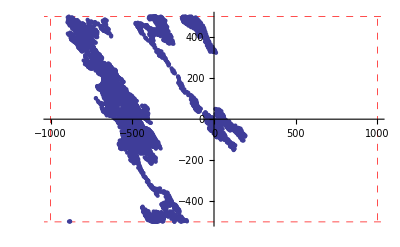

```mathematica
$VerbosePrint = True;
$VerboseLevel = 3;
AbsoluteTiming[
 rw = ParallelGenerateDiffusionTrajectory2D[STEPS=40000 , DIFFX, DIFFY, DIFFA, ENERGY, KT, STEP, {-CELLRANGE, CELLRANGE}, Verbose -> True,"VerboseLevel"->5, "InitialPositions" -> {{0, 0}, {0, 0}}, "ProcessCount" -> 1];
 ]


w = {250, 125}*1;(*width of bin*)
w0 = {0, 0}; (*lower left point of bin*)
ListPlot[rw[[All, ;; ;; Ceiling[STEPS/10000], {2, 3}]], PlotRange -> Transpose@{-CELLRANGE, CELLRANGE}, GridLines -> Transpose@{-CELLRANGE, CELLRANGE}, GridLinesStyle -> Directive[Red, Thick, Dashed],
 Epilog -> {Opacity[0], EdgeForm[{Red, Thick}], Rectangle[w0 - w/2, w0 + w/2]}]
```

## Analyze diffusion

```mathematica
w=CELLRANGE/.5;
binSpec=Transpose[{-CELLRANGE,CELLRANGE,w}];
AbsoluteTiming[diffs=GetDiffusionInBins[rw,STEP,binSpec,"CellRange"->{-CELLRANGE,CELLRANGE},Verbose->False,"Strides"->{1},"PadSteps"->False,Parallel->False,"ReturnStepsHistogram"->True];]
First@diffs
Dimensions@diffs
```

```mathematica
bins=GetValues[{{"x","y"},{"xWidth","yWidth"}},diffs[[All,1]]];
```

```mathematica
GetCellRangeFromBins@bins;
```

```mathematica
diffs[[All,1]]
fittedG=DrawDiffusionTensorRepresentations[diffs[[All,1]],Scale->40,"OutlineStyle"->{Black,Thick,Opacity@.5},"FillStyle"->{Black,Opacity@.5}]
```

```mathematica
actualG=DrawDiffusionTensorRepresentations[GetDiffusionInfoFromParameters[{{-2000,2000,2000/8},{-1000,1000,1000/8}},DIFFX,DIFFY,DIFFA],Scale->4,"OutlineStyle"->{Red,Thick,Opacity@.5},"FillStyle"->{Red,Opacity@.5}]
```

```mathematica
Show[actualG,fittedG,ImageSize->Large]
```

## misc

```mathematica
(*For easier storage in Git*)
SetOptions[InputNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},TrackCellChangeTimes->False];FrontEndTokenExecute["DeleteGeneratedCells"];
(*Auto delete output on close*)
```

```mathematica
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndTokenExecute["DeleteGeneratedCells"]}];
```